```mathematica
Predicting Gold Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

## Resources

- PAXG hourly price: Recent (≥ 2020) data - Gemini.

## In This Notebook

LPPLS model implementation (2026 ed.) for Gold price in USD.
Uses PAXG price as a proxy for Gold’s price, due to current lack of access to high quality (hourly) Spot Gold price data.

```mathematica
base=DirectoryName[NotebookFileName[]];
lastPriceDate=DateString[Yesterday,"ISODate"]
```

2026-01-28

```mathematica
hourlyPricesUrl="https://www.cryptodatadownload.com/cdd/Gemini_PAXGUSD_1h.csv";
prices =Import[hourlyPricesUrl, HeaderLines->1]
```

```mathematica
(* First price date: *)
firstDownloadedDateTime=prices[[-1]][[2]];
{firstDownloadedDate,firstDownloadedTime}=StringSplit[firstDownloadedDateTime];
firstPriceDate=firstDownloadedDate
```

2020-10-31

```mathematica
(* Some freshness checks: *)
lastDownloadedDateTime=prices[[2]][[2]];
{lastDownloadedDate, lastDownloadedTime}=StringSplit[lastDownloadedDateTime]
{DateString[DatePlus[lastDownloadedDate, 0], "ISODate"]==lastPriceDate, lastDownloadedTime=="23:00:00"}
```

{2026-01-28,23:00:00}

{True,True}

```mathematica
closingPrices={#[[1]],#[[7]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Convert to seconds *)
hourlyPricesTs={#[[1]]/1000, #[[2]]}&/@closingPricesFilter
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[hourlyPricesTs, First]
```

```mathematica
Length[hourlyPrices]
```

45980

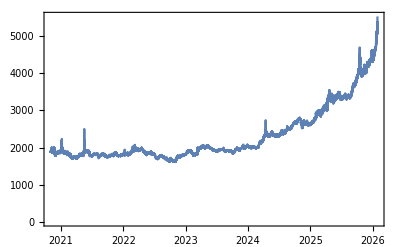

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"csv/Gold(PAXG)_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

/Users/mauro/Projects/Bitcoin/csv/Gold(PAXG)_price-hourly-20201031-20260128.csv

```mathematica
{FromUnixTime[hourlyPrices[[1]][[1]]],FromUnixTime[hourlyPrices[[-1]][[1]]]}
```

{Sat 31 Oct 2020 05:00:00GMT+1,Thu 29 Jan 2026 00:00:00GMT+1}

```mathematica
(* Use the Log Price *)
logPrice= {#[[1]], Log[#[[2]]]}&/@hourlyPrices
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2026 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2024-01-01", lastPriceDate}, {"2025-01-01", lastPriceDate}}
```

{{2024-01-01,2026-01-28},{2025-01-01,2026-01-28}}

```mathematica
bubbleN=Length[bubblesDate]
```

2

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1704063600,1769554800},{1735686000,1769554800}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{758,392}

```mathematica
bubbles=Table[Select[logPrice,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1704063600,7.61955},{1735686000,7.87335}}

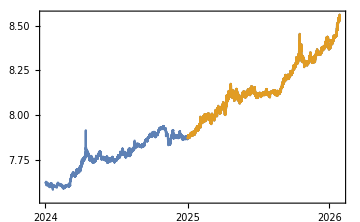

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.00016,0.996511},{1.00032,0.995062}}

```mathematica
Length/@bubblesScaled
```

{18193,9409}

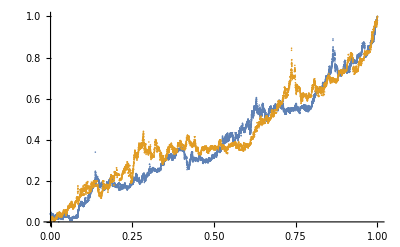

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* Export bubbles data: *)
bubbleScaledCsvs=MapIndexed[Export[base<>"csv/bubbleScaled-Gold(PAXG)"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,bubblesScaled]
```

{/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Gold(PAXG)1.tsv,/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Gold(PAXG)2.tsv}

```mathematica
(* Our "goodness of fit" control parameter. The smaller the better. i.e. stricter hypothesis testing will be. *)
(* Empirically, spans greater than 0.1 indicate that our prediction is not very reliable / trustworthy. *)bestSpan=0.09
```

0.09

```mathematica
(* Get params from R: *)
rInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@bubbleScaledCsvs;
```

```mathematica
rRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@rInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
rParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@rRuns
```

{{17.5211,18169.9},{17.5256,9385.93}}

```mathematica
(* {RSS, SE, SE of the fit}: *)
rErrors=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-6;;;;2]]&/@rRuns
```

{{5.73261,0.0177628,0.000998358},{4.26411,0.0213157,0.00165992}}

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

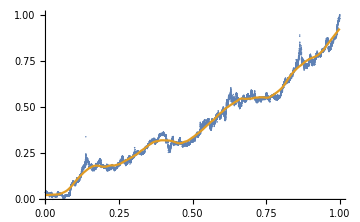
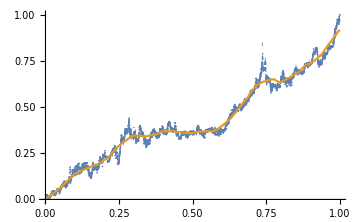

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}];
```

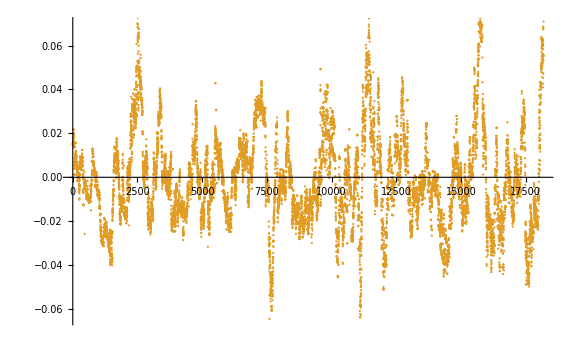
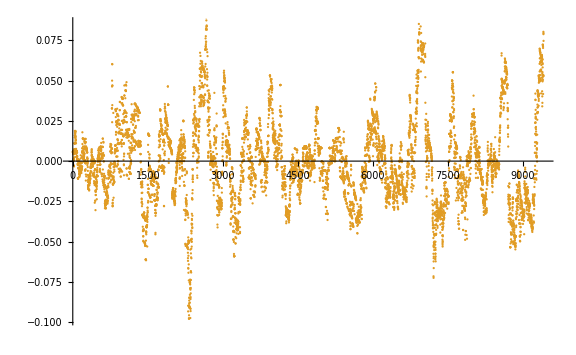

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.0212881,0.026521}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}];
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{8.25239,6.61813}

```mathematica
(* Larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[1]]]&,{ℛsSS,rErrors}]
```

{8.25239 > 5.73261,6.61813 > 4.26411}

```mathematica
(* Residual Standard Error(s): *)
ℛsSEs=MapThread[√(Total[#1^2]/(Length[#1]-#2[[1]]))&,{ℛs,rParams}]
```

{0.0213082,0.0265461}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0213082 > 0.0177628,0.0265461 > 0.0213157}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(Length[#1]-#2[[1]]))&,{ℛs,rParams, rErrors}]
```

{0.0177596,0.0213082}

```mathematica
ℛsSEs=MapThread[√(Total[#1^2]/(#2[[2]]))&,{ℛs,rParams}]
```

{0.0213115,0.0265539}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0213115 > 0.0177628,0.0265539 > 0.0213157}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(#2[[2]]))&,{ℛs,rParams, rErrors}]
```

{0.0177623,0.0213145}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Select first bubble for fitting: *)
bubble=1
```

```mathematica
(* Or, select last bubble for fitting: *)
bubble=bubbleN
```

2

```mathematica
(* Use the selected bubble: *)
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Use the params for the selected bubble: *)
{estimatedNParams, effectiveDfs}=rParams[[bubble]]
```

{17.5256,9385.93}

```mathematica
(* Profiling over 0.1 < m < 1, 3 < ω < 14 and 1. < tc < 3 months in the future *)
minM=0.1;
maxM=1;
minω=3;
maxω=14;
months=3;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
bubbleScaled[[-1]][[1]]
maxTc=bubbleScaled[[-1]][[1]]+(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.00032

2.22991

```mathematica
(* Define 7 days resolution scaled interval step: *)
stepTc=7/bubblesDays[[bubble]]//N
```

0.0178571

```mathematica
(* Define 10 days resolution scaled initial time step *)
stepTi=10/bubblesDays[[bubble]]//N
```

0.0255102

```mathematica
(* Slow. Shortcut below *)
Now[]
fits=
Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

Thu 29 Jan 2026 13:09:02GMT+1[]

{23698.1,{{a→0.968622,b→-0.883738,c→-0.0774251,d→-0.0633188,T_1→0.,tc→1.00042,m→0.6,ω→6.4,RSS→8.6402,ℛerror→0.000918975,ℛσ→0.0303049,LL→32274.9,ρ→0.965958,σ→-0.00783938,μ→-6.64211×10^-18},{a→0.968544,b→-0.883553,c→-0.07731,d→-0.0632452,T_1→0.0255102,tc→1.00042,m→0.6,ω→6.4,RSS→8.62903,ℛerror→0.000941828,ℛσ→0.0306792,LL→31346.1,ρ→0.966011,σ→-0.00793015,μ→1.22997×10^-17},{a→0.968192,b→-0.88271,c→-0.0767316,d→-0.0630169,T_1→0.0510204,tc→1.00042,m→0.6,ω→6.4,RSS→8.60852,ℛerror→0.000964864,ℛσ→0.0310518,LL→30458.1,ρ→0.966313,σ→-0.00799136,μ→-3.11633×10^-18},{a→0.968224,b→-0.882785,c→-0.0767777,d→-0.0630618,T_1→0.0765306,tc→1.00042,m→0.6,ω→6.4,RSS→8.58519,ℛerror→0.000988849,ℛσ→0.0314351,LL→29571.2,ρ→0.96662,σ→-0.00805371,μ→2.13806×10^-17},{a→0.968564,b→-0.883855,c→-0.0834765,d→-0.0580545,T_1→0.102041,tc→1.00042,m→0.6,ω→6.5,RSS→8.36126,ℛerror→0.000990436,ℛσ→0.03146,LL→28841.6,ρ→0.967289,σ→-0.00798024,μ→-3.31567×10^-17},{a→0.923644,b→-0.87531,c→-0.0945432,d→-0.0776739,T_1→0.127551,tc→1.00042,m→0.7,ω→6.4,RSS→7.5916,ℛerror→0.000925579,ℛσ→0.0304122,LL→28115.6,ρ→0.96532,σ→-0.00793921,μ→-2.39077×10^-17},{a→0.924994,b→-0.879546,c→-0.10443,d→-0.0703383,T_1→0.153061,tc→1.00042,m→0.7,ω→6.5,RSS→7.13951,ℛerror→0.000896699,ℛσ→0.0299336,LL→27327.,ρ→0.964717,σ→-0.00788067,μ→1.56411×10^-18},{a→0.924343,b→-0.877638,c→-0.103083,d→-0.0710744,T_1→0.178571,tc→1.00042,m→0.7,ω→6.5,RSS→7.05646,ℛerror→0.000913812,ℛσ→0.0302176,LL→26540.7,ρ→0.965671,σ→-0.00784902,μ→5.20083×10^-18},{a→0.925067,b→-0.879322,c→-0.0978323,d→-0.077384,T_1→0.204082,tc→1.00042,m→0.7,ω→6.4,RSS→7.00134,ℛerror→0.000935758,ℛσ→0.0305779,LL→25808.1,ρ→0.967338,σ→-0.00775067,μ→1.94224×10^-17},{a→0.92341,b→-0.874237,c→-0.0951706,d→-0.0805004,T_1→0.229592,tc→1.00042,m→0.7,ω→6.4,RSS→6.8605,ℛerror→0.000947321,ℛσ→0.0307658,LL→24877.4,ρ→0.966774,σ→-0.00786426,μ→-1.98754×10^-17},{a→0.961288,b→-0.861327,c→-0.0506787,d→-0.0964613,T_1→0.255102,tc→1.00042,m→0.6,ω→6.1,RSS→6.16617,ℛerror→0.00088063,ℛσ→0.0296627,LL→24222.1,ρ→0.966057,σ→-0.00766223,μ→-6.11536×10^-18},{a→0.960914,b→-0.859914,c→-0.0416397,d→-0.0995714,T_1→0.280612,tc→1.00042,m→0.6,ω→6.,RSS→6.06074,ℛerror→0.000896295,ℛσ→0.0299249,LL→23505.8,ρ→0.967785,σ→-0.0075339,μ→-2.3394×10^-17},{a→0.926632,b→-0.885576,c→-0.100337,d→-0.0637129,T_1→0.306122,tc→1.00042,m→0.7,ω→6.5,RSS→5.4739,ℛerror→0.000839298,ℛσ→0.0289573,LL→22870.9,ρ→0.967407,σ→-0.00733217,μ→-7.93036×10^-18},{a→1.11035,b→-1.02914,c→-0.0951707,d→-0.0151026,T_1→0.331633,tc→1.07185,m→0.6,ω→8.5,RSS→5.17717,ℛerror→0.000824128,ℛσ→0.0286939,LL→22096.6,ρ→0.967239,σ→-0.00728393,μ→-4.75348×10^-18},{a→0.957212,b→-0.848636,c→-0.0562228,d→-0.105207,T_1→0.357143,tc→1.00042,m→0.6,ω→6.1,RSS→4.83698,ℛerror→0.000800427,ℛσ→0.0282778,LL→21238.3,ρ→0.96642,σ→-0.00726586,μ→-1.87601×10^-17},{a→0.954182,b→-0.839243,c→-0.0599522,d→-0.111018,T_1→0.382653,tc→1.00042,m→0.6,ω→6.1,RSS→4.62858,ℛerror→0.000797619,ℛσ→0.0282276,LL→20376.3,ρ→0.966091,σ→-0.0072878,μ→6.21397×10^-19},{a→0.952082,b→-0.832596,c→-0.0633989,d→-0.114479,T_1→0.408163,tc→1.00042,m→0.6,ω→6.1,RSS→4.50657,ℛerror→0.000810097,ℛσ→0.0284469,LL→19550.5,ρ→0.966819,σ→-0.00726646,μ→-1.53716×10^-17},{a→0.952717,b→-0.834687,c→-0.0619578,d→-0.113887,T_1→0.433673,tc→1.00042,m→0.6,ω→6.1,RSS→4.41353,ℛerror→0.000829143,ℛσ→0.0287786,LL→18654.3,ρ→0.967001,σ→-0.00733136,μ→-1.1886×10^-17},{a→0.951327,b→-0.829975,c→-0.0654268,d→-0.11422,T_1→0.459184,tc→1.00042,m→0.6,ω→6.1,RSS→4.28516,ℛerror→0.000843038,ℛσ→0.029018,LL→17767.5,ρ→0.966716,σ→-0.00742354,μ→9.54732×10^-18},{a→0.949837,b→-0.82446,c→-0.0830554,d→-0.106123,T_1→0.484694,tc→1.00042,m→0.6,ω→6.2,RSS→4.16557,ℛerror→0.000860122,ℛσ→0.0293097,LL→16857.6,ρ→0.966545,σ→-0.00751712,μ→-9.09198×10^-18},{a→0.949292,b→-0.822113,c→-0.0971159,d→-0.09538,T_1→0.510204,tc→1.00042,m→0.6,ω→6.3,RSS→4.11589,ℛerror→0.000894176,ℛσ→0.0298833,LL→15949.6,ρ→0.966793,σ→-0.00763618,μ→6.3418×10^-18}}}

```mathematica
(* Shortcut: *)
fits=;
```

```mathematica
(* Timing in hours: *)
fits[[1]]/60/60
```

6.58279

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→1.00042 | ℛσ→0.0303049 | LL→32274.9
T_1→0.0255102 | tc→1.00042 | ℛσ→0.0306792 | LL→31346.1
T_1→0.0510204 | tc→1.00042 | ℛσ→0.0310518 | LL→30458.1
T_1→0.0765306 | tc→1.00042 | ℛσ→0.0314351 | LL→29571.2
T_1→0.102041 | tc→1.00042 | ℛσ→0.03146 | LL→28841.6
T_1→0.127551 | tc→1.00042 | ℛσ→0.0304122 | LL→28115.6
T_1→0.153061 | tc→1.00042 | ℛσ→0.0299336 | LL→27327.
T_1→0.178571 | tc→1.00042 | ℛσ→0.0302176 | LL→26540.7
T_1→0.204082 | tc→1.00042 | ℛσ→0.0305779 | LL→25808.1
T_1→0.229592 | tc→1.00042 | ℛσ→0.0307658 | LL→24877.4
T_1→0.255102 | tc→1.00042 | ℛσ→0.0296627 | LL→24222.1
T_1→0.280612 | tc→1.00042 | ℛσ→0.0299249 | LL→23505.8
T_1→0.306122 | tc→1.00042 | ℛσ→0.0289573 | LL→22870.9
T_1→0.331633 | tc→1.07185 | ℛσ→0.0286939 | LL→22096.6
T_1→0.357143 | tc→1.00042 | ℛσ→0.0282778 | LL→21238.3
T_1→0.382653 | tc→1.00042 | ℛσ→0.0282276 | LL→20376.3
T_1→0.408163 | tc→1.00042 | ℛσ→0.0284469 | LL→19550.5
T_1→0.433673 | tc→1.00042 | ℛσ→0.0287786 | LL→18654.3
T_1→0.459184 | tc→1.00042 | ℛσ→0.029018 | LL→17767.5
T_1→0.484694 | tc→1.00042 | ℛσ→0.0293097 | LL→16857.6
T_1→0.510204 | tc→1.00042 | ℛσ→0.0298833 | LL→15949.6

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

1.00382

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.00042

1.07185

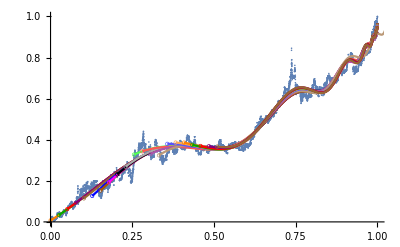

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black, Lighter[Gray], Lighter[Green], Lighter[Red], Lighter[Purple], Lighter[Brown], Lighter[Blue],Lighter[Orange]};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* 4. Rejection criteria: See if the residuals errors of the fits (ℛerror field) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.0255102,0.0510204,0.0765306,0.102041,0.127551,0.153061,0.178571,0.204082,0.229592,0.255102,0.280612,0.306122,0.331633,0.357143,0.382653,0.408163,0.433673,0.459184,0.484694,0.510204}

{0.000918975,0.000941828,0.000964864,0.000988849,0.000990436,0.000925579,0.000896699,0.000913812,0.000935758,0.000947321,0.00088063,0.000896295,0.000839298,0.000824128,0.000800427,0.000797619,0.000810097,0.000829143,0.000843038,0.000860122,0.000894176}

{8.6402,8.62903,8.60852,8.58519,8.36126,7.5916,7.13951,7.05646,7.00134,6.8605,6.16617,6.06074,5.4739,5.17717,4.83698,4.62858,4.50657,4.41353,4.28516,4.16557,4.11589}

{0.0303049,0.0306792,0.0310518,0.0314351,0.03146,0.0304122,0.0299336,0.0302176,0.0305779,0.0307658,0.0296627,0.0299249,0.0289573,0.0286939,0.0282778,0.0282276,0.0284469,0.0287786,0.029018,0.0293097,0.0298833}

```mathematica
(* Only last bubble *)
npBestFit=bestFits[[bubble]];
```

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

9409

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}];
```

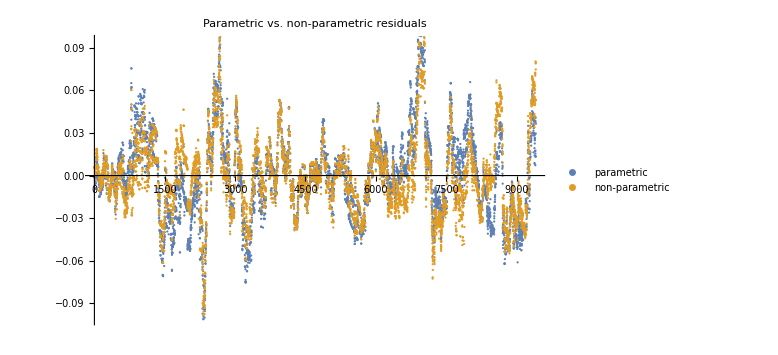

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{6.61813,8.6402}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.0265539,0.0303146}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.000705112,0.000918975}

```mathematica
selN=Length[T1s];
selN
```

21

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selNpBestFit
```

{9409,9169,8929,8689,8449,8209,7969,7729,7489,7249,7009,6769,6529,6289,6049,5809,5569,5329,5089,4849,4609}

```mathematica
selBubbleScaled2=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selBubbleScaled2
```

{9409,9169,8929,8689,8449,8209,7969,7729,7489,7249,7009,6769,6529,6289,6049,5809,5569,5329,5089,4849,4609}

```mathematica
(* Export selected bubbles: *)
selBubbleScaledCsvs=MapIndexed[Export[base<>"csv/selBubbleScaled-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,selBubbleScaled2];
```

```mathematica
selBubbleScaled=#[[All,2]]&/@selBubbleScaled2;
```

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{9409,9169,8929,8689,8449,8209,7969,7729,7489,7249,7009,6769,6529,6289,6049,5809,5569,5329,5089,4849,4609}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.000918975,0.000941828,0.000964864,0.000988849,0.000990436,0.000925579,0.000896699,0.000913812,0.000935758,0.000947321,0.00088063,0.000896295,0.000839298,0.000824128,0.000800427,0.000797619,0.000810097,0.000829143,0.000843038,0.000860122,0.000894176}

```mathematica
RSSs
```

{8.6402,8.62903,8.60852,8.58519,8.36126,7.5916,7.13951,7.05646,7.00134,6.8605,6.16617,6.06074,5.4739,5.17717,4.83698,4.62858,4.50657,4.41353,4.28516,4.16557,4.11589}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.026521,0.0268374,0.0271484,0.0274245,0.0276557,0.0277942,0.0278577,0.0279068,0.0281309,0.0284899,0.0276949,0.0273357,0.026852,0.0268436,0.0266713,0.0270445,0.0274999,0.0275484,0.0277946,0.0283442,0.0290342}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.95519,σ→-0.00784958,μ→-0.0000138575},{ρ→0.955224,σ→-0.00794033,μ→-0.0000175085},{ρ→0.955567,σ→-0.00800219,μ→-0.0000116188},{ρ→0.955782,σ→-0.0080644,μ→-2.47714×10^-6},{ρ→0.957398,σ→-0.00798574,μ→-9.33432×10^-6},{ρ→0.95868,σ→-0.00790659,μ→-0.0000293959},{ρ→0.959126,σ→-0.00788269,μ→-0.0000341164},{ρ→0.959717,σ→-0.00784041,μ→-9.2935×10^-6},{ρ→0.961349,σ→-0.0077448,μ→-0.0000218599},{ρ→0.961215,σ→-0.00785698,μ→-0.0000178755},{ρ→0.960823,σ→-0.00767547,μ→0.0000220258},{ρ→0.960824,σ→-0.00757582,μ→-0.0000206934},{ρ→0.962009,σ→-0.00733049,μ→-0.0000518729},{ρ→0.962718,σ→-0.00726076,μ→-0.0000572534},{ρ→0.961991,σ→-0.00728287,μ→-0.0000197587},{ρ→0.962744,σ→-0.00731261,μ→-0.0000287654},{ρ→0.964175,σ→-0.00729414,μ→-0.0000331665},{ρ→0.963504,σ→-0.00737387,μ→-0.0000634318},{ρ→0.963354,σ→-0.00745467,μ→-0.0000555683},{ρ→0.963797,σ→-0.00755679,μ→-0.0000414301},{ρ→0.964386,σ→-0.00767865,μ→-0.0000435948}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[-0.0000138575,{0.95519},0.0000616159],ARProcess[-0.0000175085,{0.955224},0.0000630489],ARProcess[-0.0000116188,{0.955567},0.0000640351],ARProcess[-2.47714×10^-6,{0.955782},0.0000650346],ARProcess[-9.33432×10^-6,{0.957398},0.0000637721],ARProcess[-0.0000293959,{0.95868},0.0000625142],ARProcess[-0.0000341164,{0.959126},0.0000621368],ARProcess[-9.2935×10^-6,{0.959717},0.0000614721],ARProcess[-0.0000218599,{0.961349},0.000059982],ARProcess[-0.0000178755,{0.961215},0.0000617322],ARProcess[0.0000220258,{0.960823},0.0000589129],ARProcess[-0.0000206934,{0.960824},0.000057393],ARProcess[-0.0000518729,{0.962009},0.0000537361],ARProcess[-0.0000572534,{0.962718},0.0000527187],ARProcess[-0.0000197587,{0.961991},0.0000530402],ARProcess[-0.0000287654,{0.962744},0.0000534742],ARProcess[-0.0000331665,{0.964175},0.0000532045],ARProcess[-0.0000634318,{0.963504},0.000054374],ARProcess[-0.0000555683,{0.963354},0.0000555722],ARProcess[-0.0000414301,{0.963797},0.0000571051],ARProcess[-0.0000435948,{0.964386},0.0000589617]}

{32298.1,31368.8,30480.,29592.8,28861.,28130.4,27337.1,26551.7,25818.8,24887.,24229.4,23513.5,22879.,22104.3,21239.5,20375.2,19549.9,18652.3,17765.8,16855.9,15946.9}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

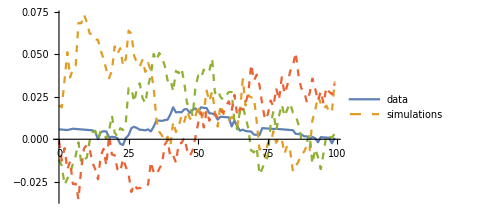
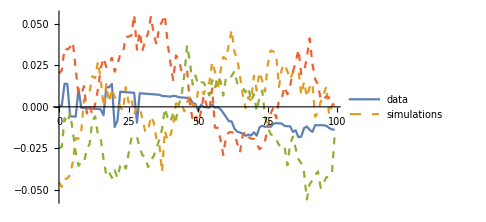
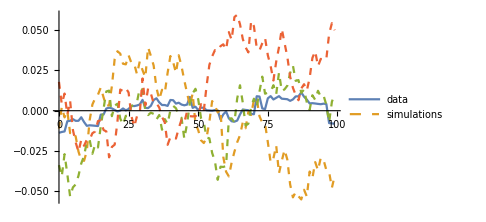
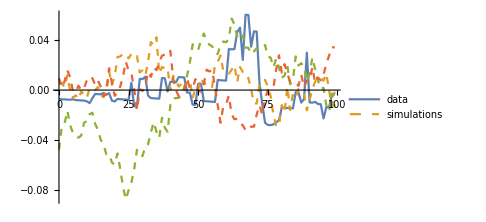
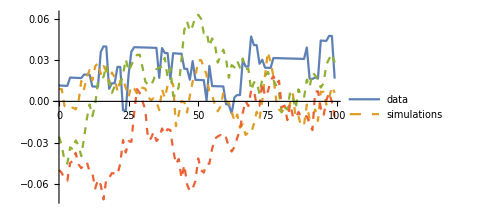
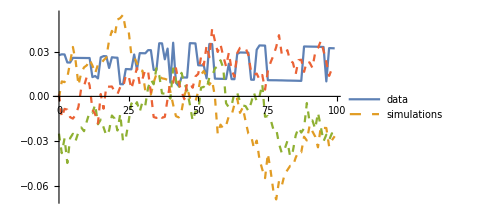
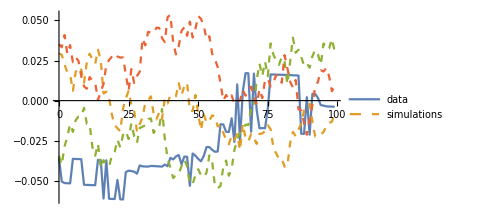
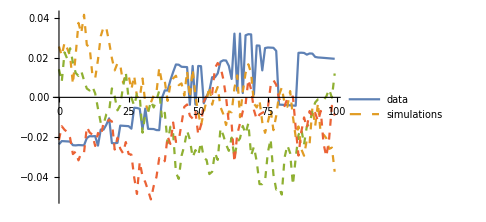

```mathematica
(* Show some simulations and data points *)
showSims=3;
showPoints=100;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess, using list of (selections) effective dfs: *)
selRInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@selBubbleScaledCsvs;
```

```mathematica
selRRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@selRInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
selRParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@selRRuns
```

{{17.5256,9385.93},{17.5337,9145.92},{17.5432,8905.9},{17.509,8665.95},{17.5184,8425.94},{17.5288,8185.92},{17.5377,7945.91},{17.5494,7705.9},{17.5094,7465.95},{17.5208,7225.93},{17.5325,6985.92},{17.5437,6745.9},{17.5571,6505.89},{17.5104,6265.95},{17.5235,6025.93},{17.5384,5785.91},{17.5515,5545.9},{17.5691,5305.87},{17.511,5065.95},{17.5282,4825.93},{17.5463,4585.91}}

```mathematica
effectiveDfs
estimatedNParams
(*selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams, {i, selN}]*)
selEffectiveDfs=Table[selRParams[[i]][[2]], {i, selN}]
```

9385.93

17.5256

{9385.93,9145.92,8905.9,8665.95,8425.94,8185.92,7945.91,7705.9,7465.95,7225.93,6985.92,6745.9,6505.89,6265.95,6025.93,5785.91,5545.9,5305.87,5065.95,4825.93,4585.91}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEffectiveDfs[[i]]&,selPaths[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 15.4322 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 15.4323 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 2329747 Kb

Memory Used: 13.2106 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{0,0,0,0,0,9,27,23,17,36,47,20,37,78,108,184,231,218,218,289,305}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.,0.,0.,0.,0.,0.009,0.027,0.023,0.017,0.036,0.047,0.02,0.037,0.078,0.108,0.184,0.231,0.218,0.218,0.289,0.305}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False}

```mathematica
(* Take the first / largest interval that is not rejected *)
firstNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

14

```mathematica
(* As a fallback (if all rejected), take the one with the min tc *)
minTc=Min[fits[[;;,6,2]]]
```

1.00042

```mathematica
minTcIndex=Select[Table[{i,fits[[i,6,2]]==minTc},{i,selN}],#[[2]]&]//First//#[[1]]&
```

1

```mathematica
index=If[NumericQ[firstNotRejectedIndex], firstNotRejectedIndex,minTcIndex]
```

14

```mathematica
selFit={fits[[index]], "index"-> index}//Flatten
```

{a→1.11035,b→-1.02914,c→-0.0951707,d→-0.0151026,T_1→0.331633,tc→1.07185,m→0.6,ω→8.5,RSS→5.17717,ℛerror→0.000824128,ℛσ→0.0286939,LL→22096.6,ρ→0.967239,σ→-0.00728393,μ→-4.75348×10^-18,index→14}

```mathematica
bestIndex=index
fit=fits[[bestIndex]]
```

14

{a→1.11035,b→-1.02914,c→-0.0951707,d→-0.0151026,T_1→0.331633,tc→1.07185,m→0.6,ω→8.5,RSS→5.17717,ℛerror→0.000824128,ℛσ→0.0286939,LL→22096.6,ρ→0.967239,σ→-0.00728393,μ→-4.75348×10^-18}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

0.6

8.5

1.07185

22096.6

```mathematica
t1=Subscript[T, 1]/.fit
```

0.331633

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

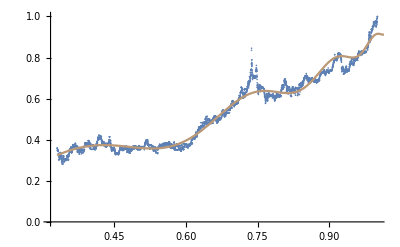

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→1.11035,b→-1.02914,c→-0.0951707,d→-0.0151026,T_1→0.331633,tc→1.07185,m→0.6,ω→8.5,RSS→5.17717,ℛerror→0.000824128,ℛσ→0.0286939,LL→22096.6,ρ→0.967239,σ→-0.00728393,μ→-4.75348×10^-18}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.967239,σ→-0.00728393,μ→-4.75348×10^-18}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

1.92007

{1.06744,1.07185}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92007

{1.06744,1.07185,1.07518}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

1.00032

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Mon 23 Feb 2026 07:15:32

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Wed 25 Feb 2026 00:43:34

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Thu 26 Feb 2026 08:01:57

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Thu 29 Jan 2026 08:55:49

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Wed 25 Feb 2026 00:43:34

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Wed 28 Jan 2026 00:56:25

```mathematica
(* For reference: *)
{#[[5]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[5]][[2]]/lastScaledTc],#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

T_1→0. | Wed 1 Jan 2025 00:00:00 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.0255102 | Fri 10 Jan 2025 23:55:24 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.0510204 | Mon 20 Jan 2025 23:50:48 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.0765306 | Thu 30 Jan 2025 23:46:13 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.102041 | Sun 9 Feb 2025 23:41:37 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.127551 | Wed 19 Feb 2025 23:37:02 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.153061 | Sat 1 Mar 2025 23:32:26 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.178571 | Tue 11 Mar 2025 23:27:51 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.204082 | Fri 21 Mar 2025 23:23:15 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.229592 | Mon 31 Mar 2025 23:18:40 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.255102 | Thu 10 Apr 2025 23:14:04 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.280612 | Sun 20 Apr 2025 23:09:29 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.306122 | Wed 30 Apr 2025 23:04:53 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.331633 | Sat 10 May 2025 23:00:18 | tc→1.07185 | Wed 25 Feb 2026 00:43:34
T_1→0.357143 | Tue 20 May 2025 22:55:42 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.382653 | Fri 30 May 2025 22:51:07 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.408163 | Mon 9 Jun 2025 22:46:31 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.433673 | Thu 19 Jun 2025 22:41:56 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.459184 | Sun 29 Jun 2025 22:37:20 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.484694 | Wed 9 Jul 2025 22:32:45 | tc→1.00042 | Wed 28 Jan 2026 00:56:25
T_1→0.510204 | Sat 19 Jul 2025 22:28:09 | tc→1.00042 | Wed 28 Jan 2026 00:56:25

```mathematica
(* Compute price at the low leg of the best Tc: *)
bestP=bestLppls[bestTc-epsilon,bestTc]
```

1.10663

```mathematica
lowCIP=bestLppls[lowCItc,bestTc]
```

1.07304

```mathematica
lastScaledP=bubbleBest[[-1]][[2]]
```

0.995062

```mathematica
lastPriceDate
```

2026-01-28

```mathematica
(* Closing price at `lastPriceDate` date: *)
latestPrice=hourlyPrices[[-1]][[2]]
```

5527.66

```mathematica
(* Plot predicted price evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVP[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestPrice/Exp[lastScaledP]]]},{i,min, max,1/8}]
```

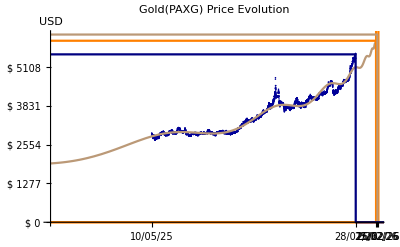

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"Gold(PAXG) Price Evolution",PlotRange->{{0,maxTc},{0,Exp[bestP]}}, Ticks->{ticksH,ticksVP},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestP+1],UnitStep[ti-highCItc]Exp[bestP+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIP],UnitStep[bestTc-ti]Exp[bestP],UnitStep[lastScaledTc-ti]Exp[lastScaledP]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/Gold(PAXG)_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

/Users/mauro/Projects/Bitcoin/png/Gold(PAXG)_PricePrediction-2026-01-28.png

```mathematica
pToPrice[p_]:= Exp[p] latestPrice/Exp[lastScaledP]
```

```mathematica
(* Check: *)
lastPrice=pToPrice[lastScaledP]
```

5527.66

```mathematica
lowCIPrice=pToPrice[lowCIP]
```

5975.96

```mathematica
bestPrice=pToPrice[bestP]
```

6180.1